## Model 1: Gaussian wave function

```mathematica
Clear[f,q,s,sb];
```

```mathematica
f["Λ/KΛ"][x_]:=(((A^2 κ^2)/(4 π^2) x(1-x) Exp[-μ^2/(4 κ^2)])/.{μ^2->1115.683^2/x+493.677^2/(1-x),κ->330,A->1.462484});
f["K/KΛ"][x_]:=(((A^2 κ^2)/(4 π^2) x(1-x) Exp[-μ^2/(4 κ^2)])/.{μ^2->1115.683^2/(1-x)+493.677^2/x,κ->330,A->1.462484});
q["s/Λ"][x_]:=(((A^2 κ^2)/(4 π^2) x(1-x) Exp[-μ^2/(4 κ^2)])/.{μ^2->480^2/x+600^2/(1-x),κ->330,A->0.230459});
q["sb/K"][x_]:=(((A^2 κ^2)/(4 π^2) x(1-x) Exp[-μ^2/(4 κ^2)])/.{μ^2->480^2/x+330^2/(1-x),κ->330,A->0.11982});
s[x_?NumberQ]:=NIntegrate[1/y f["Λ/KΛ"][y] q["s/Λ"][x/y],{y,x,1}];
sb[x_?NumberQ]:=NIntegrate[1/y f["K/KΛ"][y] q["sb/K"][x/y],{y,x,1}];
```

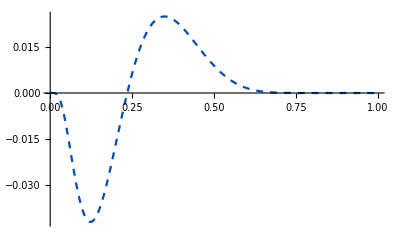

```mathematica
fig["model1"]=Plot[0.0127 (s[x]-sb[x]),{x,0.001,0.999},PlotStyle->{Dashed,RGBColor[0,0.3,0.7],Thickness[0.004]}]
```

## Model 2: Holographic wave function - I

```mathematica
Clear[f,q,s,sb];
```

```mathematica
f["Λ/KΛ"][x_]:=(((A^2 κ^2)/(16 π^2) Exp[-μ^2/κ^2])/.{μ^2->1115.683^2/x+493.677^2/(1-x),κ->350,A->3368.57});
f["K/KΛ"][x_]:=(((A^2 κ^2)/(16 π^2) Exp[-μ^2/κ^2])/.{μ^2->1115.683^2/(1-x)+493.677^2/x,κ->350,A->3368.57});
q["s/Λ"][x_]:=(((A^2 κ^2)/(16 π^2) Exp[-μ^2/κ^2])/.{μ^2->480^2/x+600^2/(1-x),κ->350,A->8.1248});
q["sb/K"][x_]:=(((A^2 κ^2)/(16 π^2) Exp[-μ^2/κ^2])/.{μ^2->480^2/x+330^2/(1-x),κ->350,A->0.900022});
s[x_?NumberQ]:=NIntegrate[1/y f["Λ/KΛ"][y] q["s/Λ"][x/y],{y,x,1}];
sb[x_?NumberQ]:=NIntegrate[1/y f["K/KΛ"][y] q["sb/K"][x/y],{y,x,1}];
```

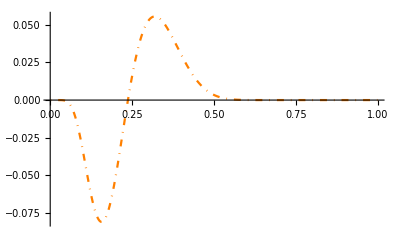

```mathematica
fig["model2"]=Plot[0.0127 (s[x]-sb[x]),{x,0.001,0.999},PlotRange->Full,PlotStyle->{DotDashed,Orange,Thickness[0.004]}]
```

## Model 3: holographic wave function - II

```mathematica
Clear[f,q,s,sb];
```

```mathematica
psi5[x_]:=(((4 π)/κ √Log[1/x] (1-x)^(1/2) Exp[-(x Log[1/x])/(2 κ^2 (1-x)) (kt^2/(x (1-x))+μ^2)]));
BM2=Simplify[Integrate[(psi5[x0]+psi5[1-x0])^2 kt/(8 π^2),{kt,0,Infinity},Assumptions->{x0>0,x0<1,κ>0,μ>0}]];
```

```mathematica
f["Λ/KΛ"][x_]:=((A^2 BM2)/.{x0->x,κ->350,A->158.815,μ^2->1115.683^2/x+493.677^2/(1-x)});
f["K/KΛ"][x_]:=((A^2 BM2)/.{x0->1-x,κ->350,A->158.815,μ^2->1115.683^2/(1-x)+493.677^2/x});
```

```mathematica
q["s/Λ"][x_]:=((A^2 (1-x) Exp[-μ^2/κ^2(x Log[1/x])/(1-x)])/.{μ^2->480^2/x+600^2/(1-x),κ->350,A->27.62368});
q["sb/K"][x_]:=((A^2 Exp[-μ^2/κ^2(x Log[1/x])/(1-x)])/.{μ^2->480^2/x+330^2/(1-x),κ->350,A->9.37766});
s[x_?NumberQ]:=NIntegrate[1/y f["Λ/KΛ"][y] q["s/Λ"][x/y],{y,x,1}];
sb[x_?NumberQ]:=NIntegrate[1/y f["K/KΛ"][y] q["sb/K"][x/y],{y,x,1}];
```

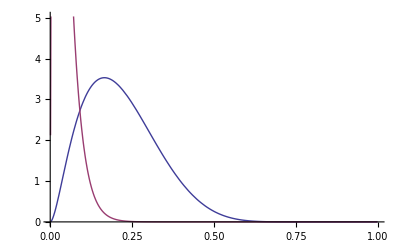

```mathematica
Plot[{s[x],sb[x]},{x,0.001,0.999},PlotPoints->20,PlotRange->Full]
```

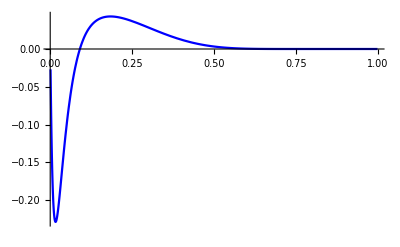

```mathematica
fig["model3"]=Plot[0.0127 (s[x]-sb[x]),{x,0.001,0.999},PlotRange->Full,PlotStyle->{Blue,Thickness[0.004]}]
```

## Plot

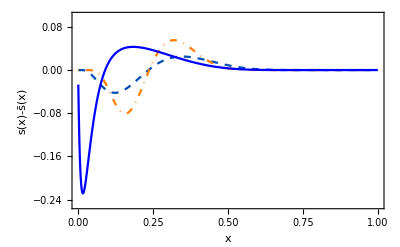

```mathematica
Show[Plot[None,{x,0,1},PlotRange->{-0.25,0.10},Frame->True,FrameLabel->{"x","s(x)-s̄(x)"}],
fig["model1"],fig["model2"],fig["model3"]]
```